```mathematica
Bez[P_,t_]:=P[[2]]+(1-t^2)(P[[1]]-P[[2]])+t^2(P[[3]])
```

```mathematica
Bern[k_,n_,x_]:=Binomial[n,k] x^k(1-x)^(n-k)
```

```mathematica
Bern[{0,1,2,3},3,t]
```

{(1-t)^3,3 (1-t)^2 t,3 (1-t) t^2,t^3}

```mathematica
Bez[P_,t_]:=Sum[Bern[k,Length[P]-1,t]*P[[k+1]],{k,0,Length[P]-1}]
```

```mathematica
Bez[{p0,p1,p2,p3},t]
```

p0 (1-t)^3+3 p1 (1-t)^2 t+3 p2 (1-t) t^2+p3 t^3

```mathematica
Pts[a_,b_]:={{0,0},{a,b},{1-a,b},{1,0}};
```

```mathematica
Bez[Pts[a,b],t]
```

{3 a (1-t)^2 t+3 (1-a) (1-t) t^2+t^3,3 b (1-t)^2 t+3 b (1-t) t^2}

```mathematica
Bez2[a_,b_,t_]:=Bez[Pts[a,b],t]
```

```mathematica
PSin[t_]:={t,Sin[π t]}
```

```mathematica
Dist2[a_,b_]:=(a[[1]]-b[[1]])^2+(a[[2]]-b[[2]])^2
```

Power::indet: Indeterminate expression 0.^0 encountered.

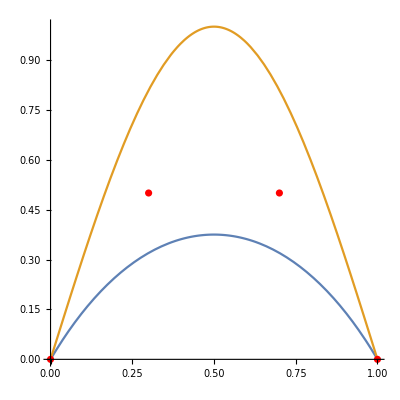

```mathematica
Show[
ParametricPlot[
{
Bez2[#1,#2,t],
PSin[t]
},{t,0,1},
PlotRange->{{0,1},{0,1}}
],
ListPlot[Pts[#1,#2],PlotStyle->Red]
]&[0.3,0.5]
```

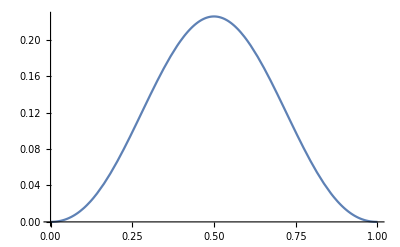

```mathematica
Plot[Dist2[
Bez2[#1,#2,t],
PSin[t]
],{t,0,1}]&[0.4,0.7]
```

```mathematica
Integrate[Dist2[
Bez2[#1,#2,t],
PSin[t]
],{t,0,1}]&[0.4,0.7]
```

0.105365

```mathematica
Minimize[{
Integrate[Dist2[
Bez2[a,b,t],
PSin[t]
],{t,0,1}],
0<a<1/2&&1/2<b<2},{a,b}
]
```

{1/210 (105-100800/π^6),{a→1/3,b→40/π^3}}

Power::indet: Indeterminate expression 0.^0 encountered.

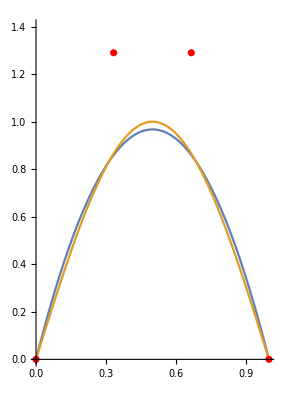

```mathematica
Show[
ParametricPlot[
{
Bez2[#1,#2,t],
PSin[t]
},{t,0,1},
PlotRange->{{0,1},{0,1.4}}
],
ListPlot[Pts[#1,#2],PlotStyle->Red]
]&[1/3,40/π^3]
```

Power::indet: Indeterminate expression 0.^0 encountered.

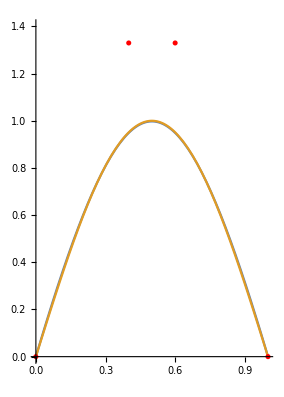

```mathematica
Show[
ParametricPlot[
{
Bez2[#1,#2,t],
PSin[t]
},{t,0,1},
PlotRange->{{0,1},{0,1.4}}
],
ListPlot[Pts[#1,#2],PlotStyle->Red]
]&[0.4,1.33]
```

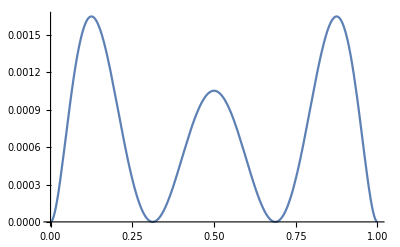

```mathematica
Plot[Dist2[
Bez2[#1,#2,t],
PSin[t]
],{t,0,1}]&[1/3,40/π^3]
```

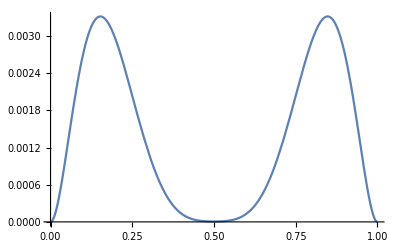

```mathematica
Plot[Dist2[
Bez2[#1,#2,t],
PSin[t]
],{t,0,1}]&[0.4,1.33]
```

```mathematica
Bez[Pts[a,b],t]
```

{3 a (1-t)^2 t+3 (1-a) (1-t) t^2+t^3,3 b (1-t)^2 t+3 b (1-t) t^2}

```mathematica
Bez3[a_,b_,t_]:={3 a (1-t)^2 t+3 (1-a) (1-t) t^2+t^3,3 b (1-t)^2 t+3 b (1-t) t^2}
```

```mathematica
Sum[
(Bez3[#1,#2,t][[2]]-Sin[π Bez3[#1,#2,t][[1]]])^2,
{t,0,1,0.1}]&[0.4,1.33]
```

0.000145403

```mathematica
NMinimize[{
Sum[
(Bez3[a,b,t][[2]]-Sin[π Bez3[a,b,t][[1]]])^2,
{t,0,1,0.0001}],
0.3<a<0.5&&1.2<b<1.5},{a,b}
]
```

{0.032283,{a→0.410331,b→1.33584}}

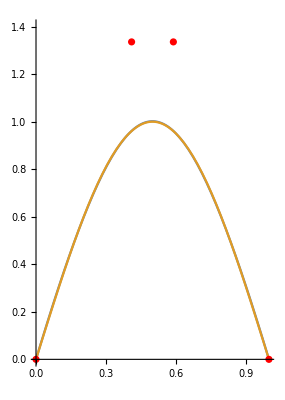

```mathematica
Show[
ParametricPlot[
{
Bez3[#1,#2,t],
PSin[t]
},{t,0,1},
PlotRange->{{0,1},{0,1.4}}
],
ListPlot[Pts[#1,#2],PlotStyle->Red]
]&[0.41033104341626886,1.3358374629527159]
```